## Lesson

/; for pattern that matches if a condition is met:

```mathematica
check[x_,y_]:=Red/;x>y
```

```mathematica
check[2,1]
```

RGBColor[1, 0, 0]

___ for pattern of any sequence of 0 or more elements:

```mathematica
{5,4,1,3,2}/. {x___,b_,a_,y___}/;b>a->{x,a,b,y}
```

{4,5,1,3,2}

.. for pattern for 1 or more repeats of pattern:

```mathematica
bwcut[{a___,Longest[(Black|White)..],b___}]:={{a},Red,{b}}
```

```mathematica
bwcut[{RGBColor[1, 0.5, 0.5],RGBColor[1, 0.5, 0.5],GrayLevel[0],GrayLevel[1],GrayLevel[1],GrayLevel[0],GrayLevel[0],RGBColor[1, 1, 0]}]
```

{{RGBColor[1, 0.5, 0.5],RGBColor[1, 0.5, 0.5]},RGBColor[1, 0, 0],{RGBColor[1, 1, 0]}}

Pattern that picks the longest sequence that matches:

```mathematica
bwcut[{a___,r:Longest[(Black|White)..],b___}]:={{a},Framed[Length[{r}]],{b}}
```

```mathematica
bwcut[{RGBColor[1, 0.5, 0.5],RGBColor[1, 0.5, 0.5],GrayLevel[0],GrayLevel[1],GrayLevel[1],GrayLevel[0],GrayLevel[0],RGBColor[1, 1, 0]}]
```

{{RGBColor[1, 0.5, 0.5],RGBColor[1, 0.5, 0.5]},5,{RGBColor[1, 1, 0]}}

Keep listing a function until the result no longer changes:

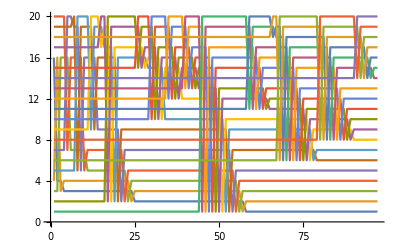

```mathematica
ListLinePlot[Transpose[FixedPointList[(#/. {x___,b_,a_,y___}/;b>a->{x,a,b,y})&,RandomSample[Range[20]]]]]
```

## Questions

Q1. Find the list of digits for squares of numbers less than 100 that contain successive repeated digits.

```mathematica
Cases[IntegerDigits[Range[100]^2],{___,x_,x_,___}]
```

{{1,0,0},{1,4,4},{2,2,5},{4,0,0},{4,4,1},{9,0,0},{1,1,5,6},{1,2,2,5},{1,4,4,4},{1,6,0,0},{2,1,1,6},{2,2,0,9},{2,5,0,0},{3,3,6,4},{3,6,0,0},{3,8,4,4},{4,2,2,5},{4,4,8,9},{4,9,0,0},{5,7,7,6},{6,4,0,0},{6,8,8,9},{7,2,2,5},{7,7,4,4},{8,1,0,0},{8,8,3,6},{1,0,0,0,0}}

Q2. In the first 100 Roman numerals, find those containing L, I and X in that order.

```mathematica
Cases[Characters[RomanNumeral[Range[100]]],{___,"L",___,"I",___,"X",___}]
```

{{X,L,I,X},{L,I,X},{L,X,I,X},{L,X,X,I,X},{L,X,X,X,I,X}}

Q3. Define a function f that tests whether a list of integers is the same as its reverse.

```mathematica
f[x:{_Integer..}]:=Reverse[x]==x
```

Q4. Get a list of pairs of successive words in the Wikipedia article on alliteration that have identical first letters.

```mathematica
Cases[Partition[TextWords[WikipediaData["alliteration"]],2,1],{a_,b_}/;ToUpperCase[StringTake[a,1]]==ToUpperCase[StringTake[b,1]]]
```

{{or,of},{It,is},{as,a},{Peter,Piper},{Piper,picked},{pickled,peppers},{of,Old},{Irish,It},{as,an},{ideas,in},{Icelandic,It},{It,is},{cartoon,characters},{the,term},{identical,initial},{several,special},{as,alliteration},{stressed,syllables},{as,an},{lazy,languid},{languid,line},{as,alliteration},{be,because},{such,syllables},{syllables,start},{consonant,clusters},{sp,st},{consonant,clusters},{s,sound},{consonant,cluster},{cluster,can},{with,words},{consonant,cluster},{s,such},{sp,st},{Walt,Whitman},{Splendid,Silent},{Silent,Sun},{consonant,clusters},{sp,st},{spit,sting},{stick,skin},{consonant,clusters},{s,seems},{same,source},{consonant,clusters},{another,Alliteration},{to,the},{the,two},{identical,in},{at,any},{home,hot},{as,a},{stressed,syllable},{humble,house},{potential,power},{power,play},{play,picture},{picture,perfect},{money,matters},{rocky,road},{quick,question},{Peter,Piper},{Piper,picked},{pickled,peppers},{of,outside},{same,sound},{of,outside},{to,the},{brown,blazers},{in,its},{Poetry,Poets},{can,call},{splendid,silent},{silent,sun},{Walt,Whitman},{Splendid,Silent},{Silent,Sun},{wondered,what},{his,horse},{by,Bernard},{also,add},{to,the},{harsh,hard},{they,than},{slippered,sleep},{lean,lithe},{fleet,flown},{E.,E.},{heaped,heartbreak},{The,tendrils},{fire,forthrightly},{Chappell,Chestnuts},{Fell,finally},{finally,finding},{Finch,Fresh-firecoal},{plotted,pieced},{fold,fallow},{plough,Pied},{Beauty,by},{height,hangs},{hangs,his},{who,wanders},{barred,by},{Who,Wanders},{We,were},{I,In},{Berkshire,bar},{workman,Who},{sat,silent},{We,Were},{swart,ship},{with,weeping},{out,onward},{canvas,Canto},{Out,of},{out,of},{to,the},{sun,sword},{An,axe},{axe,angles},{It,is},{hell's,handiwork},{silken,sad},{breeze,blew},{foam,flew},{furrow,followed},{followed,free},{stood,still},{churlish,chiding},{winter's,wind},{wind,Which},{Which,when},{brown,below},{harvests,hang},{heavy,head},{Brent,Bernard},{who,watch},{watch,with},{with,wild},{wild,wonder},{wide,window},{beautiful,birds},{birds,begin},{bountiful,birdseed},{the,Thistle},{Thurston,Three},{grey,geese},{grazing,Grey},{Grey,Geese},{Betty,Botter},{Botter,bought},{butter,but},{she,said},{butter's,bitter},{if,I},{it,in},{make,my},{batter,bitter},{bitter,but},{better,butter},{make,my},{bitter,batter},{batter,better},{the,tongue-twister},{Betty,Botter},{Botter,by},{Peter,Piper},{Piper,picked},{pickled,peppers},{Peter,Piper},{Piper,picked},{pickled,peppers},{pickled,peppers},{peppers,Peter},{Peter,Piper},{Piper,picked},{Helplessly,Hoping},{by,Bob},{throughout,the},{sun,Spieluhr},{stand,still},{stood,still},{Fairyland,Fanfare},{legend,live},{live,life},{all,alone},{to,the},{lunar,lure},{lure,Leave},{languish,Leave},{Leave,lanterns},{lorn,Lend},{Lend,lacking},{lacking,lustre},{lies,Liberate},{lone,Lest},{Lest,lament},{line,Little},{late,last},{as,an},{an,artistic},{emotional,effect},{S,sounds},{any,attitude},{is,in},{times,The},{as,an},{which,we},{our,only},{of,our},{His,help},{our,own},{but,by},{today,that},{that,the},{truths,that},{is,inextricably},{to,the},{itself,is},{testimony,to},{to,the},{have,had},{because,brave},{freedom's,front},{Ronald,Reagan},{Vietnam,Veterans},{new,nation},{to,the},{Patent,portae},{portae,proficiscere},{Ceterum,censeo},{censeo,Carthaginem},{Bleach,blonde},{blonde,bad-built},{bad-built,butch},{butch,body},{and,adds},{adds,an},{an,alliterative},{Μάρθα,Μάρθα},{Μάρθα,μεριμνᾷς},{Martha,Martha},{Martha,merimnas},{Martha,Martha},{also,Anadiplosis},{House,Handbook},{Modern,Memory},{to,the},{Some,Suggestive},{4,438},{438,45},{E,E},{55,5},{388,390},{Indolence,ISBN},{R,R},{alliteration,and},{and,alliterative},{alliterations,and}}

Q5. Use Grid to show the sorting process in this section for {4, 5, 1, 3, 2}, with successive steps going down the page.

```mathematica
Grid[FixedPointList[(#/. {x___,b_,a_,y___}/;b>a->{x,a,b,y})&,{4,5,1,3,2}]]
```

4 | 5 | 1 | 3 | 2
4 | 1 | 5 | 3 | 2
1 | 4 | 5 | 3 | 2
1 | 4 | 3 | 5 | 2
1 | 3 | 4 | 5 | 2
1 | 3 | 4 | 2 | 5
1 | 3 | 2 | 4 | 5
1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5

Q6. Use ArrayPlot to show the sorting process in this section for a list of length 50, with successive steps going across the page.

```mathematica
ArrayPlot[FixedPointList[(#/. {x___,b_,a_,y___}/;b>a->{x,a,b,y})&,RandomSample[Range[50]]]]
```

-Graphics-

Q7. Start with 1.0, then repeatedly apply the “Newton’s method” function (#+2/# )/2& until the result no longer changes.

```mathematica
FixedPointList[(#+2/#)/2&,1.0]
```

{1.,1.5,1.41667,1.41422,1.41421,1.41421,1.41421}

Q8. Implement Euclid’s algorithm for GCD in which {a, b} is repeatedly replaced by {b, Mod[a, b]} until b is 0, and apply the algorithm to 12345, 54321.

```mathematica
FixedPointList[#/. {a_,b_}/;b!=0->{b,Mod[a,b]}&,{12345,54321}]
```

{{12345,54321},{54321,12345},{12345,4941},{4941,2463},{2463,15},{15,3},{3,0},{3,0}}

Q9. Define combinators using the rules s[x_][y_][z_]→x[z][y[z]], k[x_][y_]→x, then generate a list by starting with s[s][k][s[s[s]][s]][s] and applying these rules until nothing changes.

```mathematica
FixedPointList[#/. {s[x_][y_][z_]->x[z][y[z]],k[x_][y_]->x}&,s[s][k][s[s[s]][s]][s]]
```

{s[s][k][s[s[s]][s]][s],s[s[s[s]][s]][k[s[s[s]][s]]][s],s[s[s]][s][s][k[s[s[s]][s]][s]],s[s][s][s[s]][s[s[s]][s]],s[s[s]][s[s[s]]][s[s[s]][s]],s[s][s[s[s]][s]][s[s[s]][s[s[s]][s]]],s[s[s[s]][s[s[s]][s]]][s[s[s]][s][s[s[s]][s[s[s]][s]]]],s[s[s[s]][s[s[s]][s]]][s[s][s[s[s]][s[s[s]][s]]][s[s[s[s]][s[s[s]][s]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s]][s[s[s]][s]][s[s[s[s]][s[s[s]][s]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s][s[s[s[s]][s[s[s]][s]]]][s[s[s]][s][s[s[s[s]][s[s[s]][s]]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s[s]][s][s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s]][s][s[s[s[s]][s[s[s]][s]]]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s][s[s[s[s]][s[s[s]][s]]]][s[s[s[s[s]][s[s[s]][s]]]]]][s[s[s[s]][s[s[s]][s]]][s[s][s[s[s[s]][s[s[s]][s]]]][s[s[s[s[s]][s[s[s]][s]]]]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s[s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]]]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s[s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]]]]]]]]}

Q10. Remove all trailing 0’s from the digit list for 100!.

```mathematica
IntegerDigits[100!]/.{x___,0..}->{x}
```

{9,3,3,2,6,2,1,5,4,4,3,9,4,4,1,5,2,6,8,1,6,9,9,2,3,8,8,5,6,2,6,6,7,0,0,4,9,0,7,1,5,9,6,8,2,6,4,3,8,1,6,2,1,4,6,8,5,9,2,9,6,3,8,9,5,2,1,7,5,9,9,9,9,3,2,2,9,9,1,5,6,0,8,9,4,1,4,6,3,9,7,6,1,5,6,5,1,8,2,8,6,2,5,3,6,9,7,9,2,0,8,2,7,2,2,3,7,5,8,2,5,1,1,8,5,2,1,0,9,1,6,8,6,4}

Q11. Start from {1, 0} then for 200 steps repeatedly remove the first 2 elements, and append {0, 1} if the first element is 1 and {1, 0, 0} if it is 0 and get a list of the lengths of the sequences produced (tag system).

```mathematica
Length/@NestList[#/. {{1,_,x___}->{x,0,1},{0,_,x___}->{x,1,0,0}}&,{1,0},200]
```

{2,2,3,3,4,4,5,6,6,7,8,9,9,10,11,11,12,12,13,13,14,14,15,16,16,17,17,18,19,19,20,21,22,22,23,23,24,24,25,25,26,26,27,28,29,29,30,30,31,32,32,33,33,34,35,35,36,37,37,38,38,39,40,40,41,42,43,43,44,44,45,45,46,46,47,47,48,48,49,50,50,51,52,53,53,54,55,55,56,56,57,58,58,59,59,60,61,61,62,62,63,64,64,65,66,67,67,68,69,69,70,70,71,71,72,72,73,74,74,75,76,77,77,78,78,79,79,80,80,81,82,82,83,84,85,85,86,87,87,88,88,89,89,90,90,91,92,92,93,93,94,95,95,96,97,98,98,99,100,100,101,101,102,103,103,104,104,105,106,106,107,108,109,109,110,111,111,112,112,113,113,114,114,115,116,116,117,117,118,119,119,120,121,122,122,123,123,124,124,125,125}

Q12. Start from {0, 0} then for 200 steps repeatedly remove the first 2 elements, and append {2, 1} if the first element is 0, {0} if the first element is 1, and {0, 2, 1, 2} if it is 2, and make a line plot of the lengths of the sequences produced (tag system).

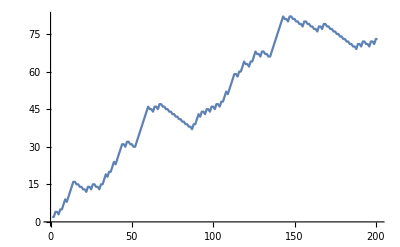

```mathematica
ListLinePlot[Length/@NestList[#/. {{0,_,x___}->{x,2,1},{1,_,x___}->{x,0},{2,_,x___}->{x,0,2,1,2}}&,{0,0},200]]
```